## Plotting Functions

Hello and welcome. Today, we are going to take a look at some of Mathematica’s plotting functionality. We’ll also look at Mathematica’s GraphicsRow function.

### Plot

Let’s take a look at the Plot function:

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i. 
Plot[{…,w[f_i],…},…] plots f_i with features defined by the symbolic wrapper w.
Plot[…,{x}∈reg] takes the variable x to be in the geometric region reg.

We start by plotting the Sine function.



```mathematica
Plot[Sin[x],{x,0,2Pi}]
```

The Plot function takes two arguments by default. In addition to arguments, it can also take options such as ImageSize that modify the behavior of the final result. We can call the function with ImageSize as follows.

You can use command+L (on mac), or ctrl+L (on windows) to insert the previous input.

Options in Mathematica are passed as rules. The syntax for a rule is: OptionName -> OptionValue.

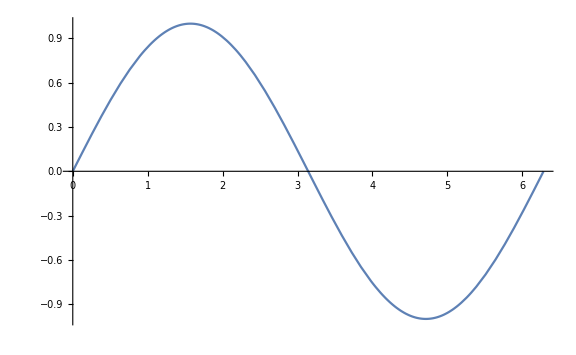

```mathematica
Plot[Sin[x],{x,0,2Pi},ImageSize->Large]
```

Let’s try plotting Cosine.

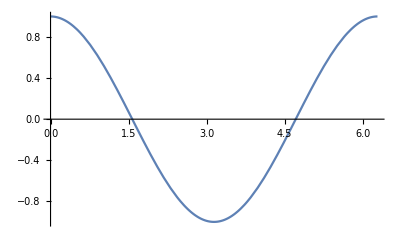

```mathematica
Plot[Cos[k],{k,0,2Pi}]
```

The variable used in the function is a dummy variable. Let’s try a more complicated function.

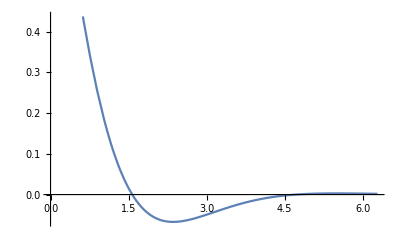

```mathematica
Plot[Exp[-x]Cos[x],{x,0,2Pi}]
```

Let’s increase the frequency of Cosine.

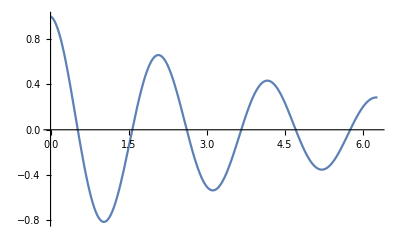

```mathematica
Plot[Exp[-0.2x]Cos[3x],{x,0,2Pi}]
```

Let's plot this function along with exponential times the sine function as well. Now we have to put two functions in the first argument of Plot. The way we do that is to turn the first argument into a list.

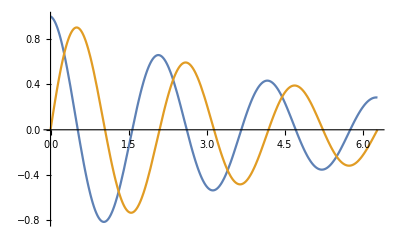

```mathematica
Plot[{Exp[-0.2x]Cos[3x],Exp[-0.2x]Sin[3x]},{x,0,2Pi}]
```

We need to add a legend to our plot to know which is which. Legend is an option to Plot.

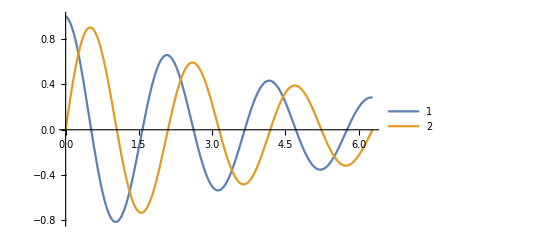

```mathematica
Plot[{Exp[-0.2x]Cos[3x],Exp[-0.2x]Sin[3x]},{x,0,2Pi},PlotLegends->Automatic]
```

Not quite useful. We have to tell it which curve is which. Our first plot is the Cosine and the second one is Sine.

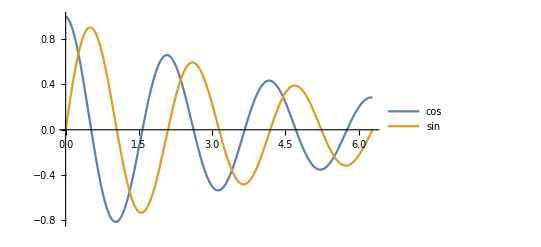

```mathematica
Plot[{Exp[-0.2x]Cos[3x],Exp[-0.2x]Sin[3x]},{x,0,2Pi},PlotLegends->{"cos","sin"}]
```

Now we need to add labels to our axes.

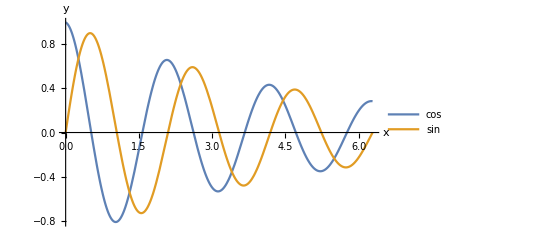

```mathematica
Plot[{Exp[-0.2x]Cos[3x],Exp[-0.2x]Sin[3x]},{x,0,2Pi},PlotLegends->{"cos","sin"},AxesLabel->{"x","y"}]
```

We can also change appearance of our plot. We can use the option PlotStyle.

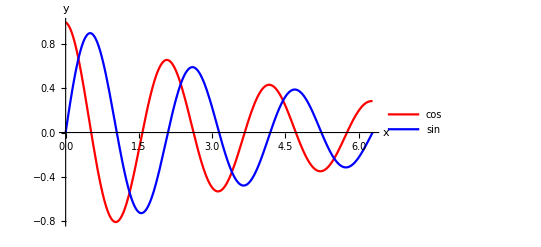

```mathematica
Plot[{Exp[-0.2x]Cos[3x],Exp[-0.2x]Sin[3x]},{x,0,2Pi},PlotLegends->{"cos","sin"},AxesLabel->{"x","y"},PlotStyle->{Red,Blue}]
```

We can modify the style even further. Let’s make the curves dashed and dotted.

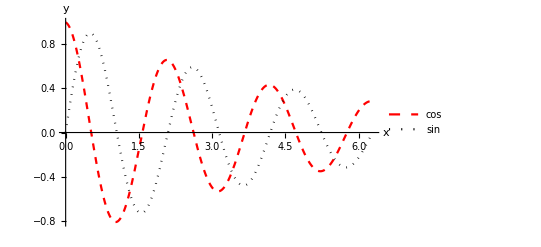

```mathematica
Plot[{Exp[-0.2x]Cos[3x],Exp[-0.2x]Sin[3x]},{x,0,2Pi},PlotLegends->{"cos","sin"},AxesLabel->{"x","y"},PlotStyle->{{Red,Dashed,Thick},{Dotted,Black}}]
```

Let’s demo something interesting. Let’s demo the following using Plot.

```mathematica
Sin[x]+Sin[x+Pi]
```

0

First we will plot the two function.

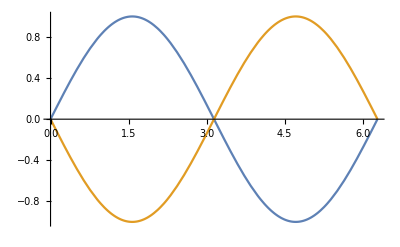

```mathematica
Plot[{Sin[x],Sin[x+Pi]},{x,0,2Pi}]
```

Now let’s try plotting {Sin[x],Sin[x+Pi]} and Sin[x]+Sin[x+Pi] next to one another using GraphicsRow.

#### GraphicsRow

A GraphicsRow is a graphics objects that allows you to have more than one plot next to one another.

```mathematica
?GraphicsRow
```

GraphicsRow[{g_1,g_2,…}] generates a graphic in which the g_i are laid out in a row.
GraphicsRow[list,spacing] leaves the specified spacing between successive elements.

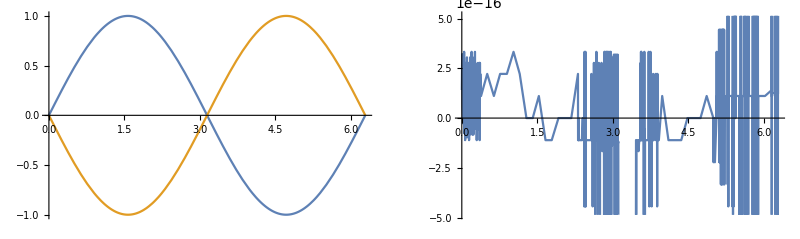

```mathematica
GraphicsRow[{Plot[{Sin[x],Sin[x+Pi]},{x,0,2Pi}],Plot[Sin[x]+Sin[x+Pi],{x,0,2Pi}]}]
```

That isn’t quite what we expected. This should have been zero. If you look at the range of this plot, you can see that the values are very very small. This must actually be numerical error during the computation of the plot. 
We need a chart where the range of the left and the right plots are the same. So what we need is to modify our plots, each one individually, to have the same plot range. We can do that using the option PlotRange.

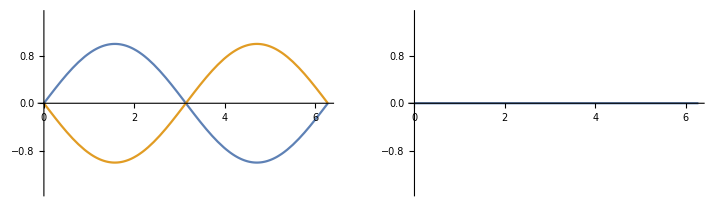

```mathematica
GraphicsRow[{Plot[{Sin[x],Sin[x+Pi]},{x,0,2Pi},PlotRange->{Automatic,{-1.5,1.5}}],Plot[Sin[x]+Sin[x+Pi],{x,0,2Pi},PlotRange->{Automatic,{-1.5,1.5}}]}]
```

Much better. Now we can see the chart on the right is zero throughout the domain. There are many options for all the functions in Mathematica. Please have a look at the options of Plot in the documentation center.

### Summary

Today we looked at the Plot function and the GraphicsRow Function, and we experimented with some options to the Plot function. We also used Mathematica to visually demonstrate Sin[x]+Sin[x+Pi]=0. We hope you had fun. See you at the next lecture.